```mathematica
ClearAll[eqs, sol,n];
m = 9; Subscript[γ, c]=2.4 10^11; Subscript[γ, s]= 1.458 10^9;
Subscript[γ, n]= 3 J 10^9; Subscript[γ, p]= 3.6 J 10^9 ; J = 1/3;
ξ = 1/10; Subscript[f, r]= 2.5 10^9; τ̃ =11.1;(*5.48;*)(* 6.48;*) (*7.45*)
τ =τ̃/Subscript[f, r]; 
IC = { n[t /; t< 0]==0.01, s[t /; t< 0]==1};
eqs= {
D[s[t],t] == (Subscript[γ, c] Subscript[γ, n])/(J Subscript[γ, s])n[t] (s[t] +1)-Subscript[γ, p] s[t](s[t]+1),
D[ n[t], t] == Subscript[γ, s] ξ(1+J)(1 + s[t-τ])-Subscript[γ, s] n[t] - Subscript[γ, s] J s[t] - Subscript[γ, n] n[t](1+s[t])+(Subscript[γ, s] Subscript[γ, p])/Subscript[γ, c] J s[t] (1+s[t])
};
Num = 100;
tMax =Num * τ; (*5 *) (* 50 -- characteristic time *)
sol = NDSolve[Join[eqs, IC], {s, n}, {t, 0., tMax}
,Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},AccuracyGoal->60,PrecisionGoal->3,MaxSteps->Infinity]⟦1⟧
S1func = s /. sol;
N1func = n /. sol;
```

{s→                                   -7
InterpolatingFunction[{{0., 4.44 10  }}, <>],n→                                   -7
InterpolatingFunction[{{0., 4.44 10  }}, <>]}

```mathematica
shift =tMax; 
IC2= { n[t /; t< 0]==S1func[90τ+t], s[t /; t< 0]==N1func[90τ+t]};
sol2 = NDSolve[Join[eqs, IC2], {s, n}, {t, 0., 10 τ}
,Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},AccuracyGoal->60,PrecisionGoal->3,MaxSteps->Infinity]⟦1⟧
S2func = s /. sol2;
N2func = n /. sol2;
```

{s→InterpolatingFunction[…],n→InterpolatingFunction[…]}

```mathematica
shift =tMax; 
IC3= { n[t /; t< 0]== S1func[89τ+t], s[t /; t< 0]==N1func[89τ+t]};
sol3 = NDSolve[Join[eqs, IC3], {s, n}, {t, 0., 10 τ}
,Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}},AccuracyGoal->60,PrecisionGoal->3,MaxSteps->Infinity]⟦1⟧
S3func = s /. sol3;
N3func = n /. sol3;
```

{s→InterpolatingFunction[…],n→InterpolatingFunction[…]}

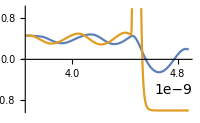

```mathematica
img = Plot[{S2func[t], S3func[t]}, {t, 0.82 τ, 1.1τ}, PlotRange->{Automatic, {-1, 1}}
, Ticks->None,  AxesLabel->{MaTeX@"\\mathrm{time}", MaTeX@"S"}, ImageSize->{200, 150}, ImagePadding->33]
Export[path<>"ics.pdf", img];
```

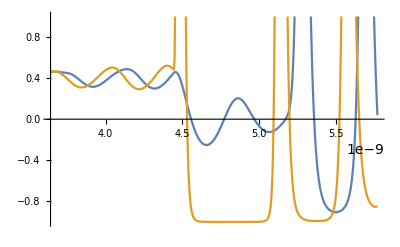

```mathematica
Plot[{S2func[t], S3func[t]}, {t, 0.82 τ, 1.3τ}, PlotRange->{Automatic, {-1, 1}}]
```

```mathematica
ClearAll[S1func, S2func, S3func, N1func, N2func, N3func];
```